# Backwards Differentiation Formulas

As always a reminder our target is to be able to understand literature such as https://en.wikipedia.org/wiki/Backward_differentiation_formula.  Of course, our real target is more involved professional literature but the Wiki page is a start.

## Example Stiff Problem

We are going to start with a simple test problem
	y'=A.y
where A is the matrix from approximating u_xx using standard centered differences.   See Rabeya’s talk for details.  For reasonable m the matrix has some large negative eigenvalues!  This means that there are some bits of the solution that decay very rapidly.   This is bad news because the ODE solvers you learnt in Calculus One will need to take tiny steps. We need solvers that can take reasonable sized steps in circumstances where there are rapidly decaying components of the solution!

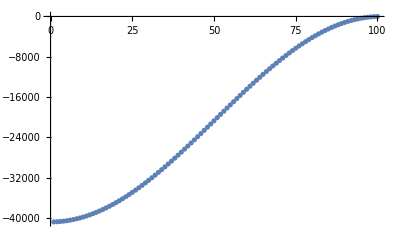

```mathematica
m=100;
A=(m+1)^2 SparseArray[{
Band[{1,1}]->-2,
Band[{1,2}]->1,
Band[{2,1}]->1},{m,m}];
ListPlot[Eigenvalues[A]]
```

For Rabeya’s test problem we should be able to explicitly compare the matrix exponential 
	ⅇ^(A t)y_0	
solution to whatever we get from our approximations.    The large negative eigenvalues (indicating fast time scales for decay) in the same problem as slower time scales are problematic.

## Explicit Euler

The Explicit Euler approximation with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is simply
	y_(k+1)=y_k+h f(k h,y_k).
For Rabeya’s test problem y'=A.y we get
	y_1=y_0+h A.y_0
organizing and repeating the process gives
	y_1 | = | (I+h A).y_0
y_2 | = | (I+h A)^2.y_0
  | ⋮ |  
y_k | = | (I+h A)^k.y_0

The question is when does this look like the matrix exponential?

## Implicit Euler

The Implicit Euler approximation aka BDF_1 with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is simply
	y_(k+1)=y_k+h f((k+1) h,y_(k+1)).
For Rabeya’s test problem y'=A.y we we get
	y_1=y_0+h A.y_1
or equivalently
	y_1=(I-h A)^-1.y_0
organizing and repeating the process gives
	y_1 | = | (I-h A)^-1.y_0
y_2 | = | (I-h A)^-2.y_0
  | ⋮ |  
y_k | = | (I-h A)^-k.y_0

The question is when does this look like the matrix exponential?

## Trapezoid aka Crank-Nicolson

A trapezoid approximation with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is called the Crank-Nicolson scheme in PDE problems.
	y_(k+1)=y_k+h/2 (f(k h,y_k)+f((k+1) h, y_(k+1))).
For Rabeya’s test problem y'=A.y we we get
	y_1=y_0+h/2 (A.y_0+A.y_1)
or equivalently
	y_1=(I-h/2 A)^-1.(I+h/2 A).y_0
organizing and repeating the process gives
	y_1 | = | ((I-h/2 A)^-1.(I+h/2 A))^1.y_0
y_2 | = | ((I-h/2 A)^-1.(I+h/2 A))^2.y_0
  | ⋮ |  
y_k | = | ((I-h/2 A)^-1.(I+h/2 A))^k.y_0
The question is when does this look like the matrix exponential?

## BDF_2 etc.

The BDF_1 (aka Implicit Euler) update formula is  
	(y_(k+1)-y_k)/h= f(t_(k+1),y_(k+1))
The left hand side is just a backwards difference approximation to the derivative.  If we use a slightly fancier approximation to the derivative we get the second of the BDF formula.
	(y_(k+2)-4/3 y_(k+1)+1/3 y_k)/(2/3 h)= f(t_(k+2),y_(k+2)).  
It may well not be obvious that the left hand side is an approximation to the derivative at some appropriate point.  It may be even less obvious that the left hand side of the next one 
	(y_(k+3)-18/11 y_(k+2)+9/11 y_(k+1)-2/11 y_K)/(6/11 h)= f(t_(k+3),y_(k+3))
is a more accurate derivative approximation!

```mathematica
f[t_]:=t+ ArcTan[t+t^2+Cos[Sin[t]]]
h=0.1;
TabView[{
"BDF_1"->Plot[{f'[t+h],(f[t+h]-f[t])/h},{t, 0,3}],
"BDF_2"->Plot[{f'[t+2h],(f[t+2h]-4/3 f[t+h]+1/3 f[t])/(2/3 h)},{t, 0,3}],
"BDF_3"->Plot[{f'[t+3h],(f[t+3h]-18/11 f[t+2h]+9/11 f[t+h]-2/11 f[t])/(6/11 h)},{t, 0,3}]
}]
```

123

We can see the asymptotic behavior.

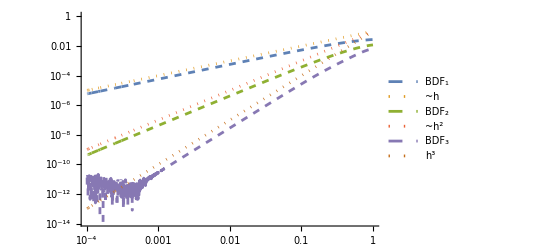

```mathematica
t0=2.1;
LogLogPlot[{
Abs[(f[t0+h]-f[t0])/h-f'[t0+h]],10^-1 h,
Abs[(f[t0+2h]-4/3 f[t0+h]+1/3 f[t0])/(2/3 h)-f'[t0+2h]],10^-1 h^2,
Abs[(f[t0+3h]-18/11 f[t0+2h]+9/11 f[t0+h]-2/11 f[t0])/(6/11 h)-f'[t0+3h]],10^-1 h^3
},{h, 10^-4,1},GridLines->Automatic,
PlotStyle->{Dashed,Dotted},
PlotLegends->{"BDF_1","~h","BDF_2","~h^2","BDF_3","h^3"}]
```

#### Taylor Series verification of error behavior

We can compute the asymptotic behavior using Taylor Series. To keep things tidy I am going to assume the ODE is autonomous. Rewrite the update formulas 
	BDF_1	y_(k+1)-y_k=h f(y_(k+1))
	BDF_2	y_(k+2)-4/3 y_(k+1)+1/3 y_k=2/3 h f(y_(k+2))
	BDF_3	y_(k+3)-18/11 y_(k+2)+9/11 y_(k+1)-2/11 y_K= 6/11 h f(y_(k+3))
about the point inside the function to get
	BDF_1	y_j-y_(j-1)=h f(y_j)
	BDF_2	y_j-4/3 y_(j-1)+1/3 y_(j-2)=2/3 h f(y_j)
	BDF_3	y_j-18/11 y_(j-1)+9/11 y_(j-2)-2/11 y_(j-3)= 6/11 h f(y_j).
If I compute the Taylor series about y_j I should be able to see the asymptotic behavior observed above
	BDF_1	(y_j-y_(j-1))/h=y'(t_j)-1/2 h y''(t_j)+O(h^2)
	BDF_2	(y_j-4/3 y_(j-1)+1/3 y_(j-2))/(2/3 h)=y'(t_j)-1/3 h^2 y^(3)(t_j)+O(h^3)
	BDF_3	(y_j-18/11 y_(j-1)+9/11 y_(j-2)-2/11 y_(j-3))/(6/11 h)= y'(t_j)-1/4 h^3 y^(4)(t_j)+O(h^4).

```mathematica
TraditionalForm[Series[ (y[Subscript[t, j]]-y[Subscript[t, j]-h])/h,{h,0,1}]]
TraditionalForm[Series[ (y[Subscript[t, j]]-4/3 y[Subscript[t, j]-h]+1/3 y[Subscript[t, j]-2h])/(2/3 h),{h,0,2}]]
TraditionalForm[Series[ (y[Subscript[t, j]]-18/11 y[Subscript[t, j]-h]+9/11 y[Subscript[t, j]-2h]-2/11 y[Subscript[t, j]-3h])/(6/11 h),{h,0,3}]]
```

y'(t_j)-1/2 h y''(t_j)+O(h^2)

y'(t_j)-1/3 h^2 y^(3)(t_j)+O(h^3)

y'(t_j)-1/4 h^3 y^(4)(t_j)+O(h^4)

#### Standard Interpolation Construction of BDF.

The polynomials that interpolate the value y_j at time t_j and the back values y_(j-1) at time t_j-h and y_(j-2) at time t_j-2h etc are
 	BDF_1	p_1(t)=y_j-((t-t_j) (y_(j-1)-y_j))/h
	BDF_2	p_2(t)= (t-t_j) (-((h-t_j+t) ((y_(j-1)-y_j)/h-(y_(j-2)-y_(j-1))/h))/(2 h)-(y_(j-1)-y_j)/h)+y_j
	BDF_3	p_3(t)=(t-t_j) ((h-t_j+t) (-((2 h-t_j+t) (((y_(j-1)-y_j)/h-(y_(j-2)-y_(j-1))/h)/(2 h)-((y_(j-2)-y_(j-1))/h-(y_(j-3)-y_(j-2))/h)/(2 h)))/(3 h)-((y_(j-1)-y_j)/h-(y_(j-2)-y_(j-1))/h)/(2 h))-(y_(j-1)-y_j)/h)+y_j
Evaluating the derivatives of these at t=t_j gives the BDF coefficients!
	BDF_1	p_1'(t_j)=(y_j-y_(j-1))/h
	BDF_2	p_2'(t_j)= (y_(j-2) - 4 y_(j-1)+3 y_j)/(2 h)
	BDF_3	p_3'(t_j)=(-2 y_(j-3)+9 y_(j-2)-18 y_(j-1)+11 y_j)/(6 h)
You could (if you wanted to) work out the higher order BDF formulas the same way.